# FRG data invoker

## input

```mathematica
Clear["Global`*"]
```

```mathematica
Lambda2=700;(*费米子真空涨落的阶段能标 (MeV)*)
mub=0;(*重子化学势 (MeV)*)
T=250;(*温度 (MeV)*)
V=50;(*体积 (fm^3)*)
n=59;(*计算分布的取点个数*)
```

## loading data and calculation

```mathematica
v=V*(1/197.33)^3;
```

```mathematica
chi1im[x_,y_]:=Import[NotebookDirectory[]<>"data/Lam"<>ToString[x]<>"/mub"<>ToString[y]<>"/chi1.dat"]
chi2im[x_,y_]:=Import[NotebookDirectory[]<>"data/Lam"<>ToString[x]<>"/mub"<>ToString[y]<>"/chi2.dat"]
chi3im[x_,y_]:=Import[NotebookDirectory[]<>"data/Lam"<>ToString[x]<>"/mub"<>ToString[y]<>"/chi3.dat"]
chi4im[x_,y_]:=Import[NotebookDirectory[]<>"data/Lam"<>ToString[x]<>"/mub"<>ToString[y]<>"/chi4.dat"]
```

```mathematica
chi1=Flatten[chi1im[Lambda2,mub]];
chi2=Flatten[chi2im[Lambda2,mub]];
chi3=Flatten[chi3im[Lambda2,mub]];
chi4=Flatten[chi4im[Lambda2,mub]];
r42=chi4/chi2;
r31=chi3/chi1;
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
chi1T[x_]:=chi1[[x]]
chi2T[x_]:=chi2[[x]]
chi3T[x_]:=chi3[[x]]
chi4T[x_]:=chi4[[x]]
r42T[x_]:=r42[[x]]
r31T[x_]:=r31[[x]](*以上的计算是导入数据的过程，上面的报错是由于磁化率的计算数据在低温区域很小所以产生的误差，不需要低温区域的数据的话可以忽略这些报错*)
```

```mathematica
If[mub==0,
b=v*T^3*1/2*chi2T[T];
bbar=v*T^3*1/2*chi2T[T];
sigma=√(v*T^3*chi2T[T]);
Ps=N[Table[PDF[SkellamDistribution[b,bbar],x],{x,-(n-1)/2,(n-1)/2}]];
Pg=N[Table[PDF[NormalDistribution[0,sigma],x],{x,-(n-1)/2,(n-1)/2}]];(*这是0化学势计算两种分布的过程，在这里我们取点是关于n=0对称的，使用者也可以根据自己的需要在这里修改计算分布的取点范围*)
P=r42T[T]*Ps+(1-r42T[T])*Pg;
,
C1gs=chi1T[T];
C1sk=chi1T[T];
C2sk=(-1+6*chi2T[T]+r31T[T]+√((1-r31T[T])/r31T[T])*√(12*chi4T[T]-r31T[T]*(-1+12*chi2T[T]+r31T[T])))/6;
C2gs=(chi2T[T]-r31T[T]*C2sk)/(1-r31T[T]);
b=v*T^3*(C1sk+C2sk)/2;
bbar=v*T^3*(C2sk-C1sk)/2;
mu=v*T^3*C1gs;
sigma=√(v*T^3*C2gs);
Ps=N[Table[PDF[SkellamDistribution[b,bbar],x],{x,-(n-1)/2,(n-1)/2}]];
Pg=N[Table[PDF[NormalDistribution[mu,sigma],x],{x,-(n-1)/2,(n-1)/2}]];(*这是0化学势计算两种分布的过程，在这里我们取点是关于n=0对称的，使用者也可以根据自己的需要在这里修改计算分布的取点范围*)
P=r31T[T]*Ps+(1-r31T[T])*Pg;];
NB=Table[i,{i,-(n-1)/2,(n-1)/2}];(*这是计算出分布所对应的NB，也就是分布函数的横坐标。如果修改了上面计算分布的取点范围，这里的范围也要改成同样的区间*)
```

## output(data and pic)

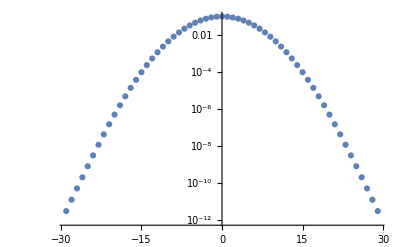

```mathematica
a=ListLogPlot[{NB,P}//Transpose]
```

```mathematica
Export[NotebookDirectory[]<>"output/"<>"P.dat",{NB,P}//Transpose,"Table"]
```

```mathematica
Export[NotebookDirectory[]<>"output/"<>"a.pdf",a,"PDF"]
```